```mathematica
SetDirectory[NotebookDirectory[]]
λ=2.0;
height=0.1;

λ=1.0;
height=0.5;

r1=0.8;
r2=0.05;
f0=10;
(*height:=r2*λ;*)
hs:=r1*height;
ks:=2*Pi/(λ);
M2=5;
g=980;
(*σ:=ρ*g*λ^2/π^2*(-1+(2*π*f0)^2*λ/(g*π*Tanh[π*r2]));*)
σ=20;

σ=72;
ρ=1.0;

A1d[q_,ks_,As_]:=Module[{κ},κ[k_, n_]:=k+n*ks;-Table[(1/2-Tanh[Norm[κ[q,n1]]*height]/2-(1/2+Tanh[Norm[κ[q,n1]]*height]/2)*(-1)^(n1-n2))*(g+σ/ρ*Norm[κ[q,n1]]^2)*Norm[κ[q,n1]]*BesselI[n1-n2,Norm[κ[q,n1]]*As]*(1-ks*(n1-n2)*κ[q,n1]/Norm[κ[q,n1]]^2),{n1,-M2,M2},{n2,-M2,M2}]]

B1d[q_,ks_,As_]:=Module[{κ},κ[k_, n_]:=k+n*ks;-Table[(1/2-Tanh[Norm[κ[q,n1]]*height]/2+(1/2+Tanh[Norm[κ[q,n1]]*height]/2)*(-1)^(n1-n2))*BesselI[n1-n2,Norm[κ[q,n1]]*As]*(1-ks*(n1-n2)*κ[q,n1]/Norm[κ[q,n1]]^2),{n1,-M2,M2},{n2,-M2,M2}]]

A2d[q_,ks_,As_,k1_,k2_]:=Module[{κ},κ[k_, n_,m_]:=k+n*ks*k1+m*ks*k2;ArrayFlatten[-Table[(1/2-Tanh[Norm[κ[q,n1,m1]]*height]/2-(1/2+Tanh[Norm[κ[q,n1,m1]]*height]/2)*(-1)^(n1-n2+m1-m2))*(g+σ/ρ*Norm[κ[q,n1,m1]]^2)*Norm[κ[q,n1,m1]]*BesselI[n1-n2,Norm[κ[q,n1,m1]]*As/2]*BesselI[m1-m2,Norm[κ[q,n1,m1]]*As/2]*(1-ks*((n1-n2)*κ[q,n1,m1].k1/Norm[κ[q,n1,m1]]^2+(m1-m2)*κ[q,n1,m1].k2/Norm[κ[q,n1,m1]]^2)),{n1,-M2,M2},{n2,-M2,M2},{m1,-M2,M2},{m2,-M2,M2}]]]

B2d[q_,ks_,As_,k1_,k2_]:=Module[{κ},κ[k_, n_,m_]:=q+n*ks*k1+m*ks*k2;ArrayFlatten[-Table[(1/2-Tanh[Norm[κ[q,n1,m1]]*height]/2+(1/2+Tanh[Norm[κ[q,n1,m1]]*height]/2)*(-1)^(n1-n2+m1-m2))*BesselI[n1-n2,Norm[κ[q,n1,m1]]*As/2]*BesselI[m1-m2,Norm[κ[q,n1,m1]]*As/2]*(1-ks*((n1-n2)*κ[q,n1,m1].k1/Norm[κ[q,n1,m1]]^2+(m1-m2)*κ[q,n1,m1].k2/Norm[κ[q,n1,m1]]^2)),{n1,-M2,M2},{n2,-M2,M2},{m1,-M2,M2},{m2,-M2,M2}]]]
```

/Users/zack/Desktop/shaker_docs/faraday

## One dimensional sinusoidal heterogeneity

```mathematica
I1[k_,As_,n1_,n2_]:=Exp[-Norm[k]*height]*BesselI[n1-n2,Norm[k]*As]
I2[k_,As_,n1_,n2_]:=Exp[Norm[k]*height]*BesselI[n1-n2,-Norm[k]*As]

A1d[q_,ks_,As_]:=Module[{κ},κ[k_, n_]:=k+n*ks;-Table[(1-ks*κ[q,n1]*(n1-n2)/Norm[κ[q,n1]]^2)*(g+σ/ρ*Norm[κ[q,n1]]^2)*Norm[κ[q,n1]]*(I1[κ[q,n1],As,n1,n2]-I2[κ[q,n1],As,n1,n2]),{n1,-M2,M2},{n2,-M2,M2}]]

B1d[q_,ks_,As_]:=Module[{κ},κ[k_, n_]:=k+n*ks;-Table[(1-ks*κ[q,n1]*(n1-n2)/Norm[κ[q,n1]]^2)*(I1[κ[q,n1],As,n1,n2]+I2[κ[q,n1],As,n1,n2]),{n1,-M2,M2},{n2,-M2,M2}]]
```

```mathematica
num=100;
sys1d[q_,A_]:={A1d[q,ks,A],B1d[q,ks,A]}
valsflat1d=Table[#^(1/2)/(2*Pi)&/@Reverse[Sort[Table[((g+σ/ρ*(Norm[t*ks/2+n*ks])^2)*(Norm[t*ks/2+n*ks])*Tanh[Norm[t*ks/2+n*ks]*height]),{n,-5,5}]]],{t,0.01,2-0.01,(1-0.01)/num}];
AbsoluteTiming[vals1d=Table[#^(1/2)/(2*Pi)&/@SingularValueList[sys1d[t*ks/2,hs]],{t,0.01,2-0.01,(1-0.01)/num}];]
```

{2.57485,Null}

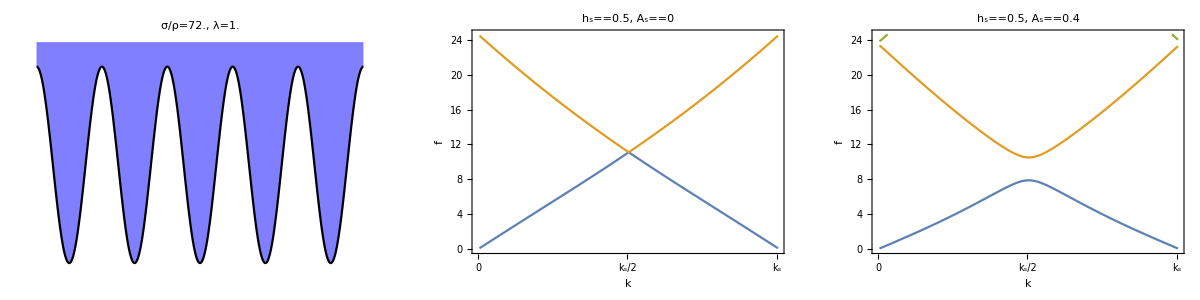

```mathematica
fmax=#^(1/2)/(2*Pi)&@((g+σ/ρ*(Norm[ks])^2)*(Norm[ks])*Tanh[Norm[ks]*height]);
p=Grid[{{Plot[hs*Cos[ks*x],{x,0,2*Pi*5/ks},PlotStyle->Black,PlotRange->{-1.1*hs,height},Axes->False,Filling->Top,FillingStyle->Directive[Opacity[0.5],Blue],ImageSize->300,PlotLabel->DisplayForm[RowBox[{"σ/ρ=",σ/ρ,", ","λ=",2*Pi/ks}]],LabelStyle->Directive[Black,16]],ListPlot[Reverse@Transpose[valsflat1d],Joined->True,PlotRange->{0,fmax},Axes->False,Frame->True,FrameLabel->{k,f},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]],FrameTicks->{{Automatic,Automatic},{{{0,0},{num,Subscript[k,s]/2},{2*num,Subscript[k,s]}},{{0,""},{num,""},{2*num,""}}}},ImageSize->300,PlotLabel->DisplayForm[RowBox[{Subscript[h,s]==height,", ", Subscript[A,s]==0}]],AspectRatio->1,ImagePadding->{{65,15},{65,15}}],
ListPlot[Reverse@Transpose[vals1d],Joined->True,PlotRange->{0,fmax},Axes->False,Frame->True,FrameLabel->{k,f},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]],FrameTicks->{{Automatic,Automatic},{{{0,0},{num,Subscript[k,s]/2},{2*num,Subscript[k,s]}},{{0,""},{num,""},{2*num,""}}}},ImageSize->300,PlotLabel->DisplayForm[RowBox[{Subscript[h,s]==height,", ", Subscript[A,s]==hs}]],AspectRatio->1,ImagePadding->{{65,15},{65,15}}]}}]
```

```mathematica
Export["1d.pdf",p]
```

### 1 d Floquet analysis and anharmonic coresonance

```mathematica
A1d[q_,ks_,As_]:=Module[{κ},κ[k_, n_]:=k+n*ks;-Table[(Norm[κ[q,n1]]-ks*κ[q,n1]*(n1-n2)/Norm[κ[q,n1]])*(g+σ/ρ*Norm[κ[q,n1]]^2)*(I1[κ[q,n1],As,n1,n2]-I2[κ[q,n1],As,n1,n2]),{n1,-M2,M2},{n2,-M2,M2}]]

B1d[q_,ks_,As_]:=Module[{κ},κ[k_, n_]:=k+n*ks;-Table[(Norm[κ[q,n1]]-ks*κ[q,n1]*(n1-n2)/Norm[κ[q,n1]])/Norm[κ[q,n1]]*(I1[κ[q,n1],As,n1,n2]+I2[κ[q,n1],As,n1,n2]),{n1,-M2,M2},{n2,-M2,M2}]]

I1[k_,As_,n1_,n2_]:=Exp[-Norm[k]*height]*BesselI[n1-n2,Norm[k]*As]
I2[k_,As_,n1_,n2_]:=Exp[Norm[k]*height]*BesselI[n1-n2,-Norm[k]*As]
A1[q_,ks_,As_,ωd_,ad_]:=Module[{κ},κ[k_, n_]:=k+n*ks;ArrayFlatten[Table[(1-ks*κ[q,n1]*(n1-n2)/Norm[κ[q,n1]]^2)*(I1[κ[q,n1],As,n1,n2]+I2[κ[q,n1],As,n1,n2])*KroneckerDelta[l1,l2],{n1,-M2,M2},{n2,-M2,M2},{l1,-M2,M2},{l2,-M2,M2}]]];
A2[q_,ks_,As_,ωd_,ad_]:=Module[{κ},κ[k_, n_]:=k+n*ks;ArrayFlatten[Table[(1-ks*κ[q,n1]*(n1-n2)/Norm[κ[q,n1]]^2)*2*I*l1*ωd*(I1[κ[q,n1],As,n1,n2]+I2[κ[q,n1],As,n1,n2])*KroneckerDelta[l1,l2],{n1,-M2,M2},{n2,-M2,M2},{l1,-M2,M2},{l2,-M2,M2}]]];
A3[q_,ks_,As_,ωd_,ad_]:=Module[{κ},κ[k_, n_]:=k+n*ks;ArrayFlatten[Table[(1-ks*κ[q,n1]*(n1-n2)/Norm[κ[q,n1]]^2)*(-ωd^2*l1^2*(I1[κ[q,n1],As,n1,n2]+I2[κ[q,n1],As,n1,n2])*KroneckerDelta[l1,l2]-(I1[κ[q,n1],As,n1,n2]-I2[κ[q,n1],As,n1,n2])*Norm[κ[q,n1]]*((g+σ/ρ*Norm[κ[q,n1]]^2)*KroneckerDelta[l1,l2]+ad/2*(KroneckerDelta[l1,l2+1]+KroneckerDelta[l1,l2-1]))),{n1,-M2,M2},{n2,-M2,M2},{l1,-M2,M2},{l2,-M2,M2}]]];
A[q_,ks_,As_,ωd_,ad_]:=ArrayFlatten[{{A3[q,ks,As,ωd,ad],A2[q,ks,As,ωd,ad]},{ConstantArray[0,{(2*M2+1)^2,(2*M2+1)^2}],IdentityMatrix[(2*M2+1)^2]}}]
B[q_,ks_,As_,ωd_,ad_]:=ArrayFlatten[{{ConstantArray[0,{(2*M2+1)^2,(2*M2+1)^2}],-A1[q,ks,As,ωd,ad]},{IdentityMatrix[(2*M2+1)^2],ConstantArray[0,{(2*M2+1)^2,(2*M2+1)^2}]}}]
sys1dfloq[q_,As_,ωd_,ad_]:={A[q,ks,As,ωd,ad],B[q,ks,As,ωd,ad]}
sys1d[q_,A_]:={A1d[q,ks,A],B1d[q,ks,A]}
```

{38.1802,Null}

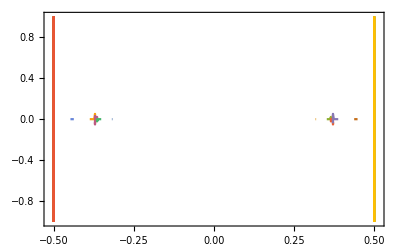

```mathematica
ωd=4.2*2*Pi;
admin=0.9*g;
admax=1.0*g;
num=10;
Monitor[AbsoluteTiming[vals=Table[Eigenvalues[sys1dfloq[ks/2,hs,ωd,ad]],{ad,admin,admax,(admax-admin)/num}];],ad/g]
ListPlot[Transpose[SortBy[{Im[#]/(ωd),Re[#]}&/@#,#[[1]]&]&/@vals,{2,1,3}],PlotRange->{{-0.51,0.51},{-1,1}},Joined->True,Axes->False,Frame->True]
```

```mathematica
ωd=5.4*2*Pi;
Cases[SortBy[{Im[#]/(ωd),Re[#]}&/@Eigenvalues[sys1dfloq[ks/2,hs,ωd,0]],#[[1]]&],u_/;u[[1]]>-0.5&&u[[1]]<0.5]
2*#^(1/2)/(2*Pi)&/@SingularValueList[sys1d[ks/2,hs]]
Min[#,1-#]&/@Mod[#^(1/2)&/@SingularValueList[sys1d[ks/2,hs]]/(ωd),1]
```

{{-0.492438,-1.5119×10^-32},{-0.460899,-4.25314×10^-15},{-0.346522,-6.2342×10^-15},{-0.336216,-7.12494×10^-13},{-0.323283,-6.35802×10^-29},{-0.310604,1.53132×10^-29},{-0.28708,2.10607×10^-14},{-0.239741,1.22807×10^-32},{0.239741,1.2281×10^-32},{0.28708,-1.88548×10^-14},{0.310604,4.29402×10^-29},{0.323283,2.26915×10^-28},{0.336216,-7.35876×10^-13},{0.346522,-1.59082×10^-15},{0.460899,-3.95101×10^-15},{0.492438,-1.51191×10^-32}}

{105.638,78.9176,73.7252,50.4535,48.242,29.3072,28.6545,14.242,14.098,5.31164,2.58594}

{0.21873,0.307188,0.173595,0.328378,0.466851,0.286372,0.346805,0.318699,0.305367,0.491818,0.239439}

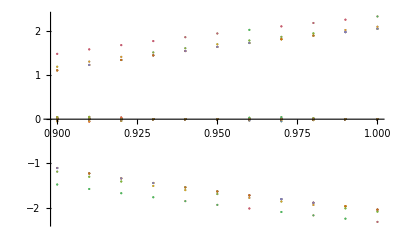

```mathematica
ListPlot[Transpose[{Table[ad/g,{ad,admin,admax,(admax-admin)/num}],#}]&/@Transpose[SortBy[{Im[#]/(ωd),Re[#]}&/@#,#[[1]]&]&/@vals,{2,1,3}][[All,All,2]],PlotRange->All]
```

```mathematica
I1[k_,As_,n1_,n2_]:=Exp[-Norm[k]*height]*BesselI[n1-n2,Norm[k]*As]
I2[k_,As_,n1_,n2_]:=Exp[Norm[k]*height]*BesselI[n1-n2,-Norm[k]*As]
B1[s_,q_,ks_,As_,ωd_]:=Module[{κ},κ[k_, n_]:=k+n*ks;ArrayFlatten[Table[(1-ks*κ[q,n1]*(n1-n2)/Norm[κ[q,n1]]^2)*((s+I*ωd*l1)^2*(I1[κ[q,n1],As,n1,n2]+I2[κ[q,n1],As,n1,n2])*KroneckerDelta[l1,l2]-(I1[κ[q,n1],As,n1,n2]-I2[κ[q,n1],As,n1,n2])*Norm[κ[q,n1]]*((g+σ/ρ*Norm[κ[q,n1]]^2)*KroneckerDelta[l1,l2])),{n1,-M2,M2},{n2,-M2,M2},{l1,-M2,M2},{l2,-M2,M2}]]];
B2[s_,q_,ks_,As_,ωd_]:=Module[{κ},κ[k_, n_]:=k+n*ks;ArrayFlatten[Table[(1-ks*κ[q,n1]*(n1-n2)/Norm[κ[q,n1]]^2)*((I1[κ[q,n1],As,n1,n2]-I2[κ[q,n1],As,n1,n2])*Norm[κ[q,n1]]*(1/2*(KroneckerDelta[l1,l2+1]+KroneckerDelta[l1,l2-1]))),{n1,-M2,M2},{n2,-M2,M2},{l1,-M2,M2},{l2,-M2,M2}]]];
sys1d2[q_,A_,ωd_]:={B1[0.01+I*ωd/2,q,ks,A,ωd],B2[0.01+I*ωd/2,q,ks,A,ωd]}

ωmin=2*2*Pi;
ωmax=8*2*Pi;
num=50;
modes=10;

AbsoluteTiming[Monitor[subharmonic1=Table[ParallelTable[{ωd/(2*2*Pi),Min[Abs[Re[Cases[Eigenvalues[sys1d2[q,0.0,ωd]]/g,u_/;Abs[Im[u]]<10^-4]]]]},{q,ks/2/modes,ks/2,ks/2/modes}],{ωd,ωmin,ωmax,(ωmax-ωmin)/num}];,N[ωd/(2*Pi)]]]
modes=10;
AbsoluteTiming[Monitor[subharmonic2=Table[ParallelTable[{ωd/(2*2*Pi),Min[Abs[Re[Cases[Eigenvalues[sys1d2[q,hs,ωd]]/g,u_/;Abs[Im[u]]<10^-4]]]]},{q,ks/2/modes,ks/2,ks/2/modes}],{ωd,ωmin,ωmax,(ωmax-ωmin)/num}];,N[ωd/(2*Pi)]]]
```

{311.624,Null}

{1112.58,Null}

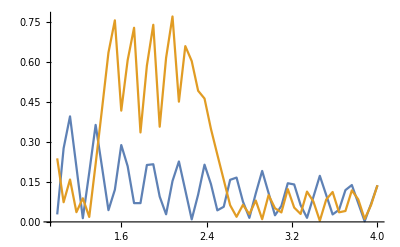

```mathematica
ListPlot[{MinimalBy[#,#[[2]]][[1]]&/@subharmonic1,MinimalBy[#,#[[2]]][[1]]&/@subharmonic2},Joined->True]
```

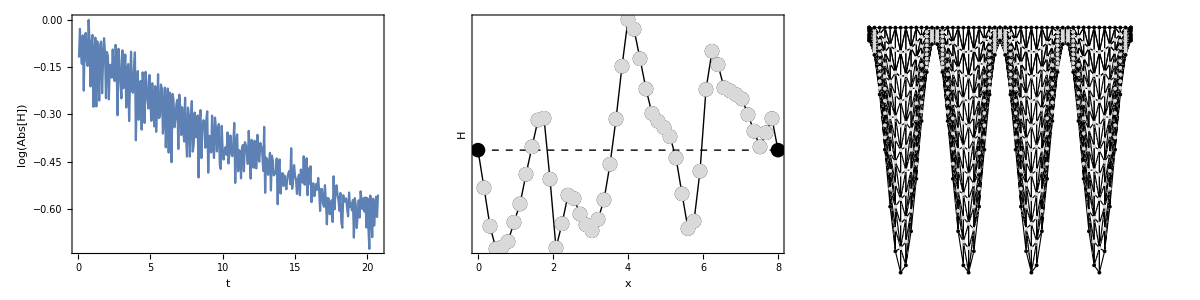

./faraday.py --filebase data/anharmonic2 --acceleration 0.3 --length 8 --frequency 2.5 --contact periodic --height 0.1 --samp 0.09 --tension 20 --damp2 0.01 --damp1 0.01 --time 50

2.500000 0.300000

```mathematica
filebase="data/anharmonic2";
lst=StringSplit[Import[filebase<>".txt"],"\n"];
meshpoints=ToExpression[lst[[FirstPosition[lst,"Mesh points"][[1]]+1]]];
mesh=Partition[Partition[BinaryReadList[filebase<>".npy","Real64"][[1+(10+BinaryReadList[filebase<>".npy","Integer16"][[5]])*8/64;;-1]],2],meshpoints];
norms=BinaryReadList[filebase<>"norms.npy","Real64"][[1+(10+BinaryReadList[filebase<>"norms.npy","Integer16"][[5]])*8/64;;-1]];
top=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Surface points coordinates"][[1]]+1]]]];
top2=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Interior surface points coordinates"][[1]]+1]]]];
length=ToExpression[lst[[FirstPosition[lst,"Length"][[1]]+1]]];
height=ToExpression[lst[[FirstPosition[lst,"Height"][[1]]+1]]];
bottom=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Substrate points coordinates"][[1]]+1]]]];
con=Partition[1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Mesh cells"][[1]]+1]]," "]],3];
contop=Cases[con,u_/;Length[Intersection[top,u]]==2];
conbottom=Cases[con,u_/;Length[Intersection[bottom,u]]==2];
sides=Flatten[Position[mesh[[-1]],u_/;Length[u]>0&&(Abs[(u[[1]]^2)^(1/2)-length]<10^-6||Abs[(u[[1]]^2)^(1/2)]<10^-6)]];
m=Length[mesh]-4;
mesh2=mesh[[m]];
Grid[{{ListPlot[Transpose[{Range[m]/15,Log[norms[[1;;m]]]/Log[10]}],Joined->True,PlotRange->All,ImageSize->350,ImagePadding->{{75,15},{75,15}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{t,Log[Abs[H]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2.0]]],Show[ListPlot[{SortBy[{#[[1]],#[[2]]-height}&/@mesh2[[top]],First],{{0,0},{length,0}}},FrameTicks->{Automatic,None},Joined->True,PlotRange->All,PlotStyle->{Directive[Black,AbsoluteThickness[1]],Directive[Black,Dashed,AbsoluteThickness[1]]},PlotRange->All,ImageSize->350,ImagePadding->{{75,15},{75,15}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{x,H},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2.0]]],ListPlot[{SortBy[{#[[1]],#[[2]]-height}&/@mesh2[[top]],First],{#[[1]],#[[2]]-height}&/@mesh2[[top2]]},FrameTicks->None,Joined->False,PlotStyle->{Directive[Black,PointSize[0.03]],Directive[LightGray,PointSize[0.03]]},PlotRange->All,ImageSize->350,ImagePadding->{{75,15},{75,15}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{x,H},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2.0]]]],
ListPlot[{mesh2,mesh2[[top]],mesh2[[sides]],mesh2[[bottom]]}, PlotStyle->{Directive[LightGray],Directive[Black],Directive[Black],Directive[Black]}, ImageSize->500,Axes->False,Frame->False,Prolog->{White,EdgeForm[Black],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@con},AspectRatio->(Max[mesh[[m,All,2]]]-Min[mesh[[m,All,2]]])/(length+2),PlotRange->{{-1,length+1},{Min[mesh[[m,All,2]]],Max[mesh[[m,All,2]]]}}]}}]
lst[[1]]
lst[[-1]]
```

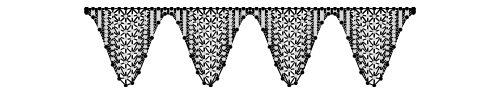

```mathematica
ListPlot[{mesh2,mesh2[[top]],mesh2[[sides]],mesh2[[bottom]]}, PlotStyle->{Directive[LightGray],Directive[Black],Directive[Black],Directive[Black]}, ImageSize->500,Axes->False,Frame->False,Prolog->{White,EdgeForm[Black],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@con},AspectRatio->10*(Max[mesh[[m,All,2]]]-Min[mesh[[m,All,2]]])/(length+2),PlotRange->{{-1,length+1},{Min[mesh[[m,All,2]]],Max[mesh[[m,All,2]]]}}]
```

#### Convergence

{6.27545,Null}

{16.5753,Null}

{35.598,Null}

{60.2859,Null}

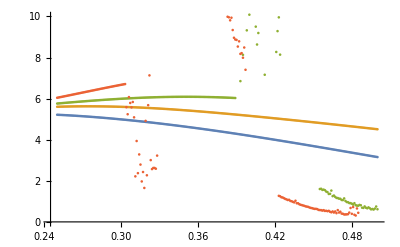

```mathematica
ks=2*Pi/(1/2);
M2=3;
AbsoluteTiming[vals1=Table[height=h;hs=height-0.05;{height,-Differences[#^(1/2)/(2*Pi)&/@SingularValueList[sys1d[ks/2,hs]]][[-1]]},{h,0.25,0.5,0.001}];]
M2=5;AbsoluteTiming[vals2=Table[height=h;hs=height-0.05;{height,-Differences[#^(1/2)/(2*Pi)&/@SingularValueList[sys1d[ks/2,hs]]][[-1]]},{h,0.25,0.5,0.001}];]
M2=7;AbsoluteTiming[vals3=Table[height=h;hs=height-0.05;{height,-Differences[#^(1/2)/(2*Pi)&/@SingularValueList[sys1d[ks/2,hs]]][[-1]]},{h,0.25,0.5,0.001}];]
M2=9;AbsoluteTiming[vals4=Table[height=h;hs=height-0.05;{height,-Differences[#^(1/2)/(2*Pi)&/@SingularValueList[sys1d[ks/2,hs]]][[-1]]},{h,0.25,0.5,0.001}];]
ListPlot[{vals1,vals2,vals3,vals4},PlotRange->{0,10}]
```

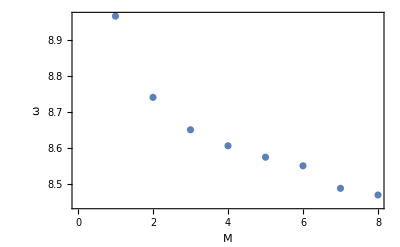

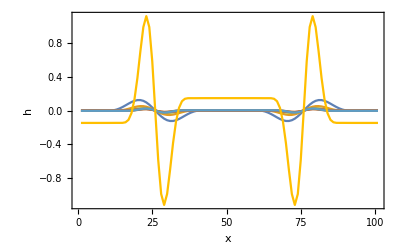

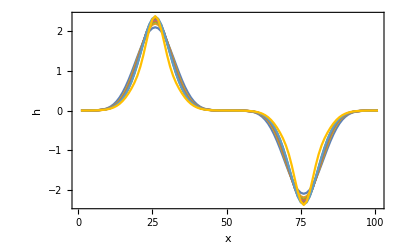

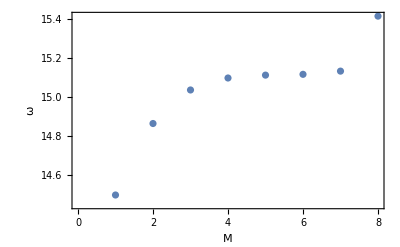

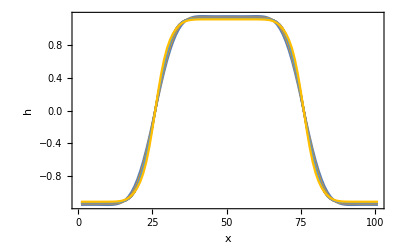

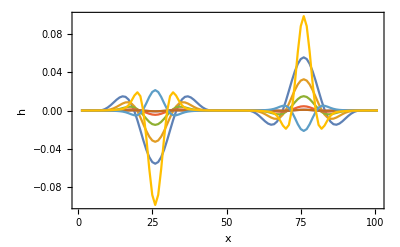

```mathematica
test=Table[Eigensystem[sysflat[ks/2,hs]],{M2,3,10}];

ListPlot[(-test[[All,1,-1]])^(1/2)/(2*Pi),Axes->False,Frame->True,FrameLabel->{M,ω},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[1]]]
test2=Table[Table[Total[test[[M2-2,2,-1]]*Sign[test[[M2-2,2,-1,M2]]]*Table[Exp[I*(κ[ks/2,n])*x],{n,-M2,M2}]],{x,-Pi/(ks/2),Pi/(ks/2),2*Pi/(ks/2)/100}],{M2,3,10}];
ListPlot[Re[test2],PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{x,h},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[1]]]
ListPlot[Im[test2],PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{x,h},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[1]]]

ListPlot[(-test[[All,1,-2]])^(1/2)/(2*Pi),Axes->False,Frame->True,FrameLabel->{M,ω},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[1]]]
test2=Table[Table[Total[test[[M2-2,2,-2]]*Sign[test[[M2-2,2,-2,M2]]]*Table[Exp[I*(κ[ks/2,n])*x],{n,-M2,M2}]],{x,-Pi/(ks/2),Pi/(ks/2),2*Pi/(ks/2)/100}],{M2,3,10}];
ListPlot[Re[test2],PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{x,h},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[1]]]
ListPlot[Im[test2],PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{x,h},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[1]]]
```

## Square heterogeneity

```mathematica
num=25;
k1={0,1};
k2={1,0};
syssquare[q_,A_]:={A2d[q,ks,A,k1,k2],B2d[q,ks,A,k1,k2]};
vals1flatsquare=Table[q=t*ks*k1/2;#^(1/2)/(2*Pi)&/@Reverse[Sort[Flatten[Table[(g+σ/ρ*(Norm[n*ks*k1+m*ks*k2+q])^2)*(Norm[n*ks*k1+m*ks*k2+q])*Tanh[Norm[n*ks*k1+m*ks*k2+q]*height],{n,-M2,M2},{m,-M2,M2}],1]]],{t,0.01,1-0.01,(1-2*0.01)/(num-1)}];
vals2flatsquare=Table[q=ks*k1/2+t*ks*((k1+k2)/2-k1/2);#^(1/2)/(2*Pi)&/@Reverse[Sort[Flatten[Table[(g+σ/ρ*(Norm[n*ks*k1+m*ks*k2+q])^2)*(Norm[n*ks*k1+m*ks*k2+q])*Tanh[Norm[n*ks*k1+m*ks*k2+q]*height],{n,-M2,M2},{m,-M2,M2}],1]]],{t,0,1-0.01,(1-0.01)/(num-1)}];
vals3flatsquare=Table[q=ks*(k1+k2)/2*(1-t);#^(1/2)/(2*Pi)&/@Reverse[Sort[Flatten[Table[(g+σ/ρ*(Norm[n*ks*k1+m*ks*k2+q])^2)*(Norm[n*ks*k1+m*ks*k2+q])*Tanh[Norm[n*ks*k1+m*ks*k2+q]*height],{n,-M2,M2},{m,-M2,M2}],1]]],{t,0,1-0.01,(1-0.01)/(num-1)}];
AbsoluteTiming[vals1square=Table[q=t*ks*k1/2;#^(1/2)/(2*Pi)&/@SingularValueList[syssquare[q,hs]],{t,0.01,1-0.01,(1-2*0.01)/(num-1)}];]
AbsoluteTiming[vals2square=Table[q=ks*k1/2+t*ks*((k1+k2)/2-k1/2);#^(1/2)/(2*Pi)&/@SingularValueList[syssquare[q,hs]],{t,0,1-0.01,(1-0.01)/(num-1)}];]
AbsoluteTiming[vals3square=Table[q=ks*(k1+k2)/2*(1-t);#^(1/2)/(2*Pi)&/@SingularValueList[syssquare[q,hs]],{t,0,1-0.01,(1-0.01)/(num-1)}];]
```

{10.1296,Null}

{10.1587,Null}

{10.1088,Null}

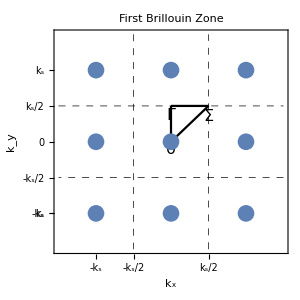
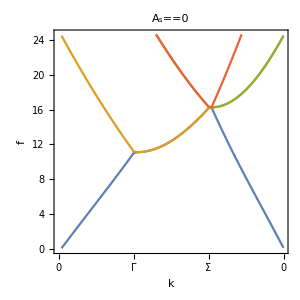
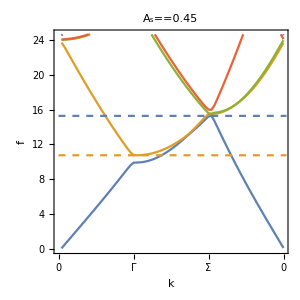
-Graphics3D- | -Graphics- | -Graphics- | -Graphics-

```mathematica
k1={0,1};
k2={1,0};
fmax=#^(1/2)/(2*Pi)&@((g+σ/ρ*(Norm[ks*k2])^2)*(Norm[ks*k2])*Tanh[Norm[ks*k2]*height]);
p=Grid[{{ListPlot3D[Flatten[Table[{x,y,1/2*(hs*Sin[ks*{x,y}.k1]+hs*Sin[ks*{x,y}.k2])},{x,0,2*Pi*5/ks,2*Pi*5/ks/100},{y,0,2*Pi*5/ks,2*Pi*5/ks/100}],1],PlotRange->{-hs,height},Boxed->False,Axes->False,Filling->Top,FillingStyle->Directive[Opacity[0.5],Blue],ImageSize->300,PlotLabel->DisplayForm[RowBox[{"σ/ρ=",σ/ρ,", ","λ=",2*Pi/ks}]],LabelStyle->Directive[Black,16]],Show[ParametricPlot[{ks*(k2/2+t*k1),-ks*(k2/2+t*k1),ks*(k1/2+t*k2),-ks*(k1/2+t*k2)},{t,-1.5,1.5},PlotStyle->Directive[Black,Dashed,AbsoluteThickness[0.5]],Axes->False,Frame->True,FrameLabel->{Subscript[k,x],Subscript[k,y]},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]],PlotRange->{{-3/2*ks,3/2*ks},{-3/2*ks,3/2*ks}},ImageSize->300,FrameTicks->{{{{-ks,Subscript[k,s]},{-ks,-Subscript[k,s]},{-ks/2,-Subscript[k,s]/2},{0,0},{ks/2,Subscript[k,s]/2},{ks,Subscript[k,s]}},{{-ks,""},{-ks,""},{-ks/2,""},{0,""},{ks/2,""},{ks,""}}},{{{-ks,-Subscript[k,s]},{-ks,-Subscript[k,s]},{-ks/2,-Subscript[k,s]/2},{0,0},{ks/2,Subscript[k,s]/2},{ks,Subscript[k,s]}},{{-ks,""},{-ks,""},{-ks/2,""},{0,""},{ks/2,""},{ks,""}}}},ImagePadding->{{65,15},{65,15}},PlotLabel->"First Brillouin Zone"],ParametricPlot[{t*ks*k1/2,ks*k1/2+t*ks*((k1+k2)/2-k1/2),ks*(k1+k2)/2*(1-t)},{t,0,1},PlotStyle->Directive[Black],Axes->False,Frame->True,FrameLabel->{Subscript[k,x],Subscript[k,y]},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]],PlotRange->{{-ks,ks},{-ks,ks}},PlotLabels->Placed[{0,Γ,Σ},Scaled[0]]],ListPlot[Flatten[Table[ks*(n*k1+m*k2),{n,-M2,M2},{m,-M2,M2}],1],AspectRatio->1,PlotRange->{{-2,2},{-2,2}},Axes->False,Frame->True,PlotStyle->Directive[PointSize[0.04]]]],ListPlot[Reverse[Transpose[Join[vals1flatsquare,vals2flatsquare,vals3flatsquare]]],PlotLabel->Subscript[A,s]==0,Joined->True,PlotRange->{0,fmax},Axes->False,Frame->True,FrameLabel->{k,f},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]],FrameTicks->{{Automatic,Automatic},{{{0,0},{num,"Γ"},{2*num,"Σ"},{3*num,0}},{{0,""},{num,""},{2*num,""},{3*num,""}}}},ImageSize->300,AspectRatio->1,ImagePadding->{{65,15},{65,15}}],
Show[ListPlot[Reverse[Transpose[Join[vals1square,vals2square,vals3square]]],PlotLabel->Subscript[A,s]==hs,Joined->True,PlotRange->{0,fmax},Axes->False,Frame->True,FrameLabel->{k,f},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]],FrameTicks->{{Automatic,Automatic},{{{0,0},{num,"Γ"},{2*num,"Σ"},{3*num,0}},{{0,""},{num,""},{2*num,""},{3*num,""}}}},ImageSize->300,AspectRatio->1,ImagePadding->{{65,15},{65,15}}],Plot[{Max[Transpose[Join[vals1square,vals2square,vals3square]][[-1,All]]],Min[Transpose[Join[vals1square,vals2square,vals3square]][[-2,All]]]},{x,0,3*num+1},Filling->Filling->Max[Transpose[Join[vals1square,vals2square,vals3square]][[-1,All]]]<Min[Transpose[Join[vals1square,vals2square,vals3square]][[-2,All]]],PlotStyle->Dashed]]}}]
```

```mathematica
Export["square.pdf",p]
```

square.pdf

## Hexagonal heterogeneity

```mathematica
num=25;
ks=2*Pi;
k1={1,-1/3^(1/2)}/(2/3^(1/2));
k2={0,2/3^(1/2)}/(2/3^(1/2));
syshex[q_,A_]:={A2d[q,ks,A,k1,k2],B2d[q,ks,A,k1,k2]};
vals1flathex=Table[q=t*ks*k1/2;#^(1/2)/(2*Pi)&/@Reverse[Sort[Flatten[Table[(g+σ/ρ*(Norm[n*ks*k1+m*ks*k2+q])^2)*(Norm[n*ks*k1+m*ks*k2+q])*Tanh[Norm[n*ks*k1+m*ks*k2+q]*height],{n,-M2,M2},{m,-M2,M2}],1]]],{t,0.01,1-0.01,(1-2*0.01)/(num-1)}];
vals2flathex=Table[q=ks*k1/2+t*ks*((2*k1+k2)/3-k1/2);#^(1/2)/(2*Pi)&/@Reverse[Sort[Flatten[Table[(g+σ/ρ*(Norm[n*ks*k1+m*ks*k2+q])^2)*(Norm[n*ks*k1+m*ks*k2+q])*Tanh[Norm[n*ks*k1+m*ks*k2+q]*height],{n,-M2,M2},{m,-M2,M2}],1]]],{t,0,1-0.01,(1-0.01)/(num-1)}];
vals3flathex=Table[q=ks*(2*k1+k2)/3*(1-t);#^(1/2)/(2*Pi)&/@Reverse[Sort[Flatten[Table[(g+σ/ρ*(Norm[n*ks*k1+m*ks*k2+q])^2)*(Norm[n*ks*k1+m*ks*k2+q])*Tanh[Norm[n*ks*k1+m*ks*k2+q]*height],{n,-M2,M2},{m,-M2,M2}],1]]],{t,0,1-0.01,(1-0.01)/(num-1)}];
AbsoluteTiming[vals1hex=Table[q=t*ks*k1/2;#^(1/2)/(2*Pi)&/@SingularValueList[syshex[q,hs]],{t,0.01,1-0.01,(1-2*0.01)/(num-1)}];]
AbsoluteTiming[vals2hex=Table[q=ks*k1/2+t*ks*((2*k1+k2)/3-k1/2);#^(1/2)/(2*Pi)&/@SingularValueList[syshex[q,hs]],{t,0,1-0.01,(1-0.01)/(num-1)}];]
AbsoluteTiming[vals3hex=Table[q=ks*(2*k1+k2)/3*(1-t);#^(1/2)/(2*Pi)&/@SingularValueList[syshex[q,hs]],{t,0,1-0.01,(1-0.01)/(num-1)}];]
```

{146.178,Null}

{142.088,Null}

{148.793,Null}

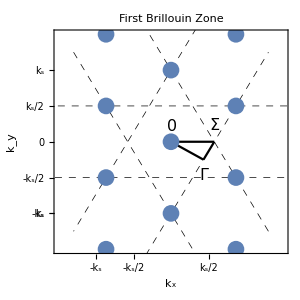
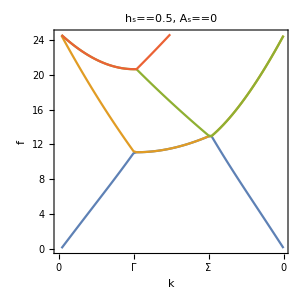
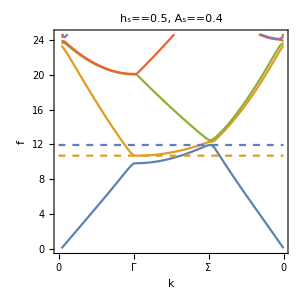
-Graphics3D- | -Graphics- | -Graphics- | -Graphics-

```mathematica
fmax=#^(1/2)/(2*Pi)&@((g+σ/ρ*(Norm[ks*k1])^2)*(Norm[ks*k1])*Tanh[Norm[ks*k1]*height]);
p=Grid[{{ListPlot3D[Flatten[Table[{x,y,1/2*(hs*Sin[ks*{x,y}.k1]+hs*Sin[ks*{x,y}.k2])},{x,0,2*Pi*5/ks,2*Pi*5/ks/100},{y,0,2*Pi*5/ks,2*Pi*5/ks/100}],1],PlotRange->{-hs,height},Boxed->False,Axes->False,Filling->Top,FillingStyle->Directive[Opacity[0.5],Blue],ImageSize->300,PlotLabel->DisplayForm[RowBox[{"σ/ρ=",σ/ρ,", ","λ=",2*Pi/ks}]],LabelStyle->Directive[Black,16]],Show[ParametricPlot[{ks*(k1+t*(k2-k1)),ks*(k1+k2+t*(-k1-(k1+k2))),-ks*(k1+t*(k2-k1)),-ks*(k1+k2+t*(-k1-(k1+k2))),ks*(k2+t*(-k1-2*k2)),-ks*(k2+t*(-k1-2*k2))},{t,-0.5,1.5},PlotStyle->Directive[Black,Dashed,AbsoluteThickness[0.5]],Axes->False,Frame->True,FrameLabel->{Subscript[k,x],Subscript[k,y]},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]],PlotRange->{{-3/2*ks,3/2*ks},{-3/2*ks,3/2*ks}},ImageSize->300,FrameTicks->{{{{-ks,Subscript[k,s]},{-ks,-Subscript[k,s]},{-ks/2,-Subscript[k,s]/2},{0,0},{ks/2,Subscript[k,s]/2},{ks,Subscript[k,s]}},{{-ks,""},{-ks,""},{-ks/2,""},{0,""},{ks/2,""},{ks,""}}},{{{-ks,-Subscript[k,s]},{-ks,-Subscript[k,s]},{-ks/2,-Subscript[k,s]/2},{0,0},{ks/2,Subscript[k,s]/2},{ks,Subscript[k,s]}},{{-ks,""},{-ks,""},{-ks/2,""},{0,""},{ks/2,""},{ks,""}}}},ImagePadding->{{65,15},{65,15}},PlotLabel->"First Brillouin Zone"],ParametricPlot[{t*ks*k1/2,ks*k1/2+t*ks*((2*k1+k2)/3-k1/2),ks*(2*k1+k2)/3*(1-t)},{t,0,1},PlotStyle->Directive[Black],Axes->False,Frame->True,FrameLabel->{Subscript[k,x],Subscript[k,y]},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]],PlotRange->{{-ks,ks},{-ks,ks}},PlotLabels->Placed[{0,Γ,Σ},Scaled[0]]],ListPlot[Flatten[Table[ks*(n*k1+m*k2),{n,-M2,M2},{m,-M2,M2}],1],AspectRatio->1,PlotRange->{{-2,2},{-2,2}},Axes->False,Frame->True,PlotStyle->Directive[PointSize[0.04]]]],ListPlot[Reverse[Transpose[Join[vals1flathex,vals2flathex,vals3flathex]]],PlotLabel->DisplayForm[RowBox[{Subscript[h,s]==height,", ", Subscript[A,s]==0}]],Joined->True,PlotRange->{0,fmax},Axes->False,Frame->True,FrameLabel->{k,f},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]],FrameTicks->{{Automatic,Automatic},{{{0,0},{num,"Γ"},{2*num,"Σ"},{3*num,0}},{{0,""},{num,""},{2*num,""},{3*num,""}}}},ImageSize->300,AspectRatio->1,ImagePadding->{{65,15},{65,15}}],
Show[ListPlot[Reverse[Transpose[Join[vals1hex,vals2hex,vals3hex]]],PlotLabel->DisplayForm[RowBox[{Subscript[h,s]==height,", ", Subscript[A,s]==hs}]],Joined->True,PlotRange->{0,fmax},Axes->False,Frame->True,FrameLabel->{k,f},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]],FrameTicks->{{Automatic,Automatic},{{{0,0},{num,"Γ"},{2*num,"Σ"},{3*num,0}},{{0,""},{num,""},{2*num,""},{3*num,""}}}},ImageSize->300,AspectRatio->1,ImagePadding->{{65,15},{65,15}}],Plot[{Max[Transpose[Join[vals1hex,vals2hex,vals3hex]][[-1,All]]],Min[Transpose[Join[vals1hex,vals2hex,vals3hex]][[-2,All]]]},{x,0,3*num},Filling->Max[Transpose[Join[vals1hex,vals2hex,vals3hex]][[-1,All]]]<Min[Transpose[Join[vals1hex,vals2hex,vals3hex]][[-2,All]]],PlotStyle->Dashed]]}}]
```

```mathematica
Export["hexagonal_tuned.pdf",p]
```

hexagonal_tuned.pdf

## Optimal parameters for hexagonal gap

```mathematica
f0=10;
λmin=0.25;
λmax=1.0;
rmin=0.15;
rmax=0.25;
num=10;
σs=Flatten[Table[λ=λmin+i*(λmax-λmin)/num;r2=rmin+j*(rmax-rmin)/num; {λ,r2,σ},{i,1,num},{j,1,num}],1];
cases=Cases[σs,u_/;u[[3]]>0&&u[[3]]<100][[All,{1,2}]];
AbsoluteTiming[Monitor[gaps=Table[λ=cases[[i,1]];r2=cases[[i,2]];k1={1,-1/3^(1/2)};
k2={0,2/3^(1/2)};
syshex[q_,A_]:={A2d[q,ks,A,k1,k2],B2d[q,ks,A,k1,k2]};
q=ks*k1/2;
freqs1=#^(1/2)/(2*Pi)&/@SingularValueList[syshex[q,hs]];
q=ks*(2*k1+k2)/3;
freqs2=#^(1/2)/(2*Pi)&/@SingularValueList[syshex[q,hs]];
{λ,r2,Min[{freqs1[[-2]],freqs2[[-2]]}]-Max[{freqs1[[-1]],freqs2[[-1]]}]},{i,1,Length[cases]}];,{i,Length[cases]}]]
```

{78.4103,Null}

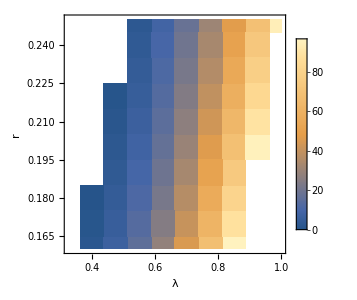
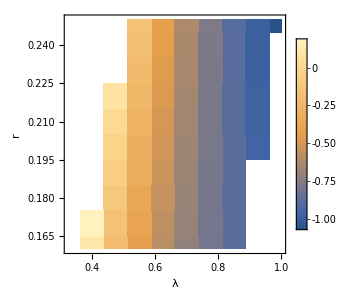
-Graphics- | -Graphics-

{{0.4,0.18,0.283754}}

```mathematica
gaps2=σs;
gaps2[[All,3]]=-10;
indices=First/@Position[σs,u_/;Length[u]>0&&u[[3]]>0&&u[[3]]<100];
gaps2[[indices]]=gaps;

Grid[{{ListDensityPlot[σs,PlotRange->{All,All,{0,100}},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]],FrameLabel->{"λ","r"},InterpolationOrder->0,PlotLegends->True,ImageSize->300],ListDensityPlot[gaps2,LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]],FrameLabel->{"λ","r"},PlotLegends->True,InterpolationOrder->0,PlotRange->{All,All,{-5,All}},ImageSize->300]}}]
MaximalBy[gaps,#[[3]]&]
```

```mathematica
gaps2=σs;
gaps2[[All,3]]=-2;
gaps2[[indices]]=gaps;
indices2=First/@Position[gaps2,u_/;Length[u]>0&&u[[3]]>0];
Join[#[[1]],{#[[2]]}]&/@Transpose[{σs[[indices2]],gaps2[[indices2]][[All,3]]}]
```

{{0.4,0.16,1.6671,0.118703},{0.4,0.17,0.794427,0.19337},{0.4,0.18,0.0271837,0.283754},{0.475,0.21,1.19721,0.0360122},{0.475,0.22,0.387799,0.100394}}

```mathematica
λ=0.4;
r2=0.18;
{σ,height,λ}
sys1d[q_,A_]:={A1d[q,ks,A],B1d[q,ks,A]}
freqs=#^(1/2)/(2*Pi)&/@SingularValueList[sys1d[ks/2,hs]];
{freqs[[-2]]-freqs[[-1]],(freqs[[-2]]+freqs[[-1]])/2}

k1={0,1};
k2={1,0};
syssquare[q_,A_]:={A2d[q,ks,A,k1,k2],B2d[q,ks,A,k1,k2]}
q=ks*k1/2;
freqs1=#^(1/2)/(2*Pi)&/@SingularValueList[syssquare[q,hs]];
q=ks*(k1+k2)/2;
freqs2=#^(1/2)/(2*Pi)&/@SingularValueList[syssquare[q,hs]];
Min[{freqs1[[-2]],freqs2[[-2]]}]-Max[{freqs1[[-1]],freqs2[[-1]]}]

k1={1,-1/3^(1/2)};
k2={0,2/3^(1/2)};
syshex[q_,A_]:={A2d[q,ks,A,k1,k2],B2d[q,ks,A,k1,k2]};
q=ks*k1/2;
freqs1=#^(1/2)/(2*Pi)&/@SingularValueList[syshex[q,hs]];
q=ks*(2*k1+k2)/3;
freqs2=#^(1/2)/(2*Pi)&/@SingularValueList[syshex[q,hs]];
Min[{freqs1[[-2]],freqs2[[-2]]}]-Max[{freqs1[[-1]],freqs2[[-1]]}]
```

{0.0271837,0.072,0.4}

{4.46712,7.57193}

-1.8685

0.283754